# Model serology with different FOI functions

## Define a partial differential equation for the general case

s[a,t] gives the probability an individual of age a has negative serology at time t and λ is the force of infection (FOI).

Arbitrary force of infection:

```mathematica
PDE = D[s[a,t],t]==-λ[t]*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==-s[a,t] λ[t]-s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE,s[0,t]==1},s[a,t],{a,t}]//FullSimplify
```

{{s[a,t]→ⅇ^(--λ[-a+t+K[1]]K[1]10+-λ[-a+t+K[1]]K[1]1a)}}

## Define a partial differential equation for the when FOI is constant

Constant force of infection:

```mathematica
PDE2 = D[s[a,t],t]==-λ*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==-λ s[a,t]-s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE2, s[0,t]==1},s[a,t],{a,t}]
```

{{s[a,t]→ⅇ^(-a λ)}}

This solution is the starting condition (i.e. S[a,0]==Exp[-λ0 a]) for t=0 for all future models. This is because we assume that FOI in the past was constant and the current conditions are now changing the FOI. For all models below t>0.

## Define a partial differential equation for the when FOI is linear

Constant force of infection:

```mathematica
PDE3 = D[s[a,t],t]==-(λ0 + λ*t)*s[a,t] - D[s[a,t],a]
```

s^(0,1)[a,t]==(-t λ-λ0) s[a,t]-s^(1,0)[a,t]

Solve the PDE assuming all individuals are born (a=0) with the probability of being susceptible =1 (i.e. s[0,t]==1).

```mathematica
DSolve[{PDE3, s[0,t]==1},s[a,t],{a,t}]
```

{{s[a,t]→ⅇ^(1/2 a (a λ-2 (t λ+λ0)))}}

NOTE: PDE3 is not solvable when we add the condition S[a,0]==Exp[-λ0 a]).

## Changing FOI from constant FOI at t=0

## FOI has a starting value for λ0 and changes to a new constant value λ

When t=0 the FOI is equal to λ0:

```mathematica
mysol=DSolve[{PDE2, s[0,t]==1,s[a,0]==Exp[-λ0 a]},s[a,t],{a,t}]//FullSimplify
```

{{s[a,t]→ⅇ^(-a (λ+λ0)) (-ⅇ^(a λ+t (-λ+λ0)) (-1+HeavisideTheta[-a+t])+ⅇ^(a λ0) HeavisideTheta[-a+t])}}

```mathematica
pars1={λ0->.01,λ->.1};
```

```mathematica
Plot3D[s[a,t]/.mysol/.pars1,{t,0,10},{a,0,70} ,AxesLabel->Automatic];
```

```mathematica
t0=s[a,t]/.mysol/.pars1/.t->0;
```

```mathematica
t5=s[a,t]/.mysol/.pars1/.t->5;
```

```mathematica
t10=s[a,t]/.mysol/.pars1/.t->10;
```

```mathematica
t15=s[a,t]/.mysol/.pars1/.t->15;
```

```mathematica
t20=s[a,t]/.mysol/.pars1/.t->20;
```

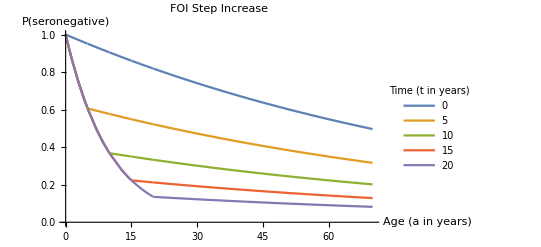

```mathematica
Plot[{t0,t5,t10,t15,t20},{a,0,70},PlotLegends->LineLegend[{"0","5","10","15","20"}, LegendLabel->"Time (t in years)"],PlotRange->{0,1},
	PlotLabel->"FOI Step Increase", AxesLabel->{"Age (a in years)","P(seronegative)"}]
```

```mathematica
MyLegend=LineLegend[{CMYKColor[0.89,0.5,0.5,0.25],CMYKColor[0.11,0.14,0.92,0.16],CMYKColor[0.08,0.8,0.74,0.39],Gray},{"0","5","10","15","20"}, LegendLabel->"Time (t in years)",LegendMarkerSize->10,LabelStyle->8]
```

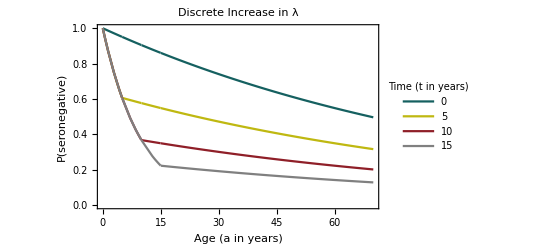

```mathematica
Pincrease=Plot[{t0,t5,t10,t15},{a,0,70},PlotStyle->{CMYKColor[0.89,0.5,0.5,0.25],CMYKColor[0.11,0.14,0.92,0.16],CMYKColor[0.08,0.8,0.74,0.39],Gray},Frame->True,FrameStyle->{{Thin,Black},{Thin,Black},{Thin,Black},{Thin,Black}},BaseStyle->{FontSize->14,FontColor->Black},FrameLabel->{"Age (a in years)","P(seronegative)"},LabelStyle->{FontColor->Black},PlotRange->{0,1},Epilog->{Inset[MyLegend,{63,0.77}]},PlotLabel->"Discrete Increase in λ"]
```

```mathematica
pars2={λ0->0.1, λ->0.01};
```

```mathematica
d0=s[a,t]/.mysol/.pars2/.t->0;
```

```mathematica
d5=s[a,t]/.mysol/.pars2/.t->5;
```

```mathematica
d10=s[a,t]/.mysol/.pars2/.t->10;
```

```mathematica
d15=s[a,t]/.mysol/.pars2/.t->15;
```

```mathematica
d20=s[a,t]/.mysol/.pars2/.t->20;
```

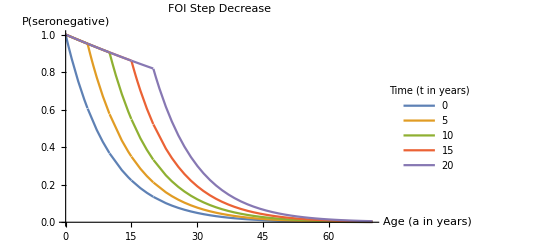

```mathematica
Plot[{d0,d5,d10,d15,d20},{a,0,70},PlotLegends->LineLegend[{"0","5","10","15","20"}, LegendLabel->"Time (t in years)"],PlotRange->{0,1},
	PlotLabel->"FOI Step Decrease", AxesLabel->{"Age (a in years)","P(seronegative)"}]
```

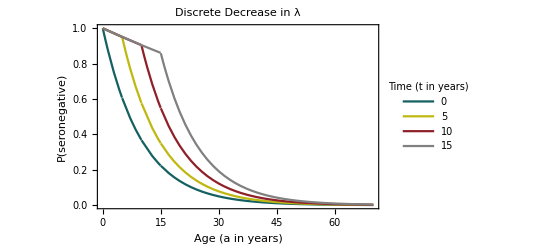

```mathematica
Pdecrease=Plot[{d0,d5,d10,d15},{a,0,70},PlotStyle->{CMYKColor[0.89,0.5,0.5,0.25],CMYKColor[0.11,0.14,0.92,0.16],CMYKColor[0.08,0.8,0.74,0.39],Gray},Frame->True,FrameStyle->{{Thin,Black},{Thin,Black},{Thin,Black},{Thin,Black}},BaseStyle->{FontSize->14,FontColor->Black},FrameLabel->{"Age (a in years)","P(seronegative)"},LabelStyle->{FontColor->Black},PlotRange->{0,1},Epilog->{Inset[MyLegend,{63,0.77}]},PlotLabel->"Discrete Decrease in λ"]
```

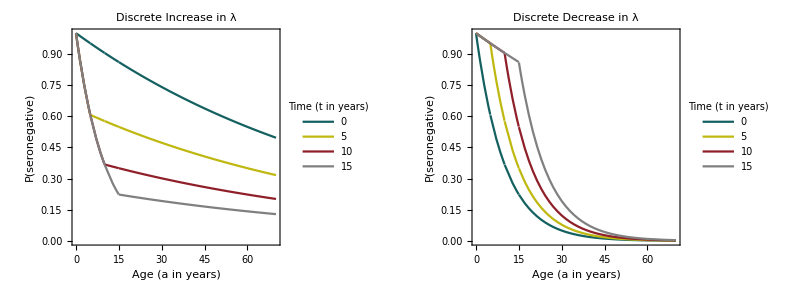

```mathematica
Figure3=GraphicsRow[{Pincrease,Pdecrease},ImageSize->800,Spacings->0]
```

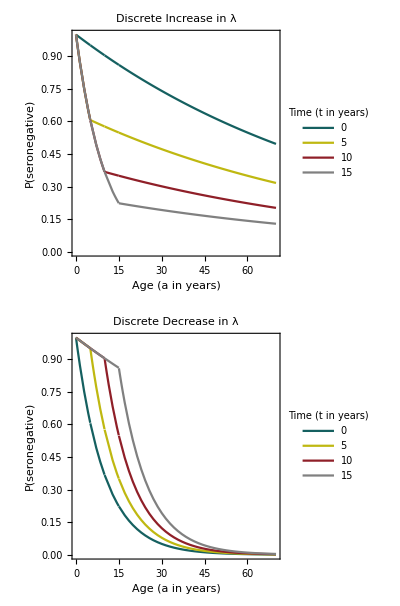

```mathematica
PrelimResults=GraphicsColumn[{Pincrease,Pdecrease},ImageSize->400,Spacings->0]
```

```mathematica
Export["Users\erin.clancey\Documents\FOI_eMB Grant\Figure3.png",Figure3]
```

Users\erin.clancey\Documents\FOI_eMB Grant\Figure3.png

#### Check Equation 2 Cucunubá et al.

```mathematica
Patau=Exp[-(λ1 (a-(τ-ξ1))+λ2 (τ-ξ1))]
```

ⅇ^(-λ1 (a+ξ1-τ)-λ2 (-ξ1+τ))

```mathematica
parscheck={λ1->0.01, λ2->0.1, ξ1->5, τ->10};
```

```mathematica
Ppars=Patau/.parscheck
```

ⅇ^(-0.5-0.01 (-5+a))

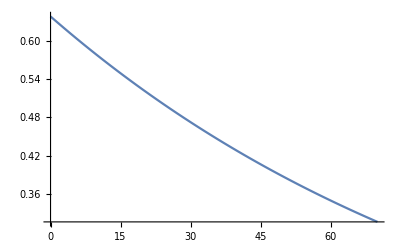

```mathematica
Plot[Patau/.parscheck,{a,0,70}]
```

```mathematica
Integrate[λ,{t,τ-a,τ}]
```

a λ

```mathematica
piece=Piecewise[{{λ1,t<ξ1},{λ2,t>ξ1}}]
```

Piecewise[{{λ1, t<ξ1}, {λ2, t>ξ1}, {0, True}}]

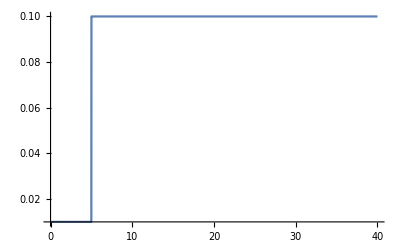

```mathematica
Plot[piece/.parscheck,{t,0,40}]
```

```mathematica
Integrate[λ1,{t,τ-a,ξ1}]+Integrate[λ2,{t,ξ1,τ}]
```

λ1 (a+ξ1-τ)+λ2 (-ξ1+τ)

## FOI has a constant starting value λ0 and changes linearly over time with slope λ

```mathematica
NumSol1=NDSolve[{PDE3,s[0,t]==1,s[a,0]==Exp[-λ0 a]}/.pars1,s[a,t],{a,0,80},{t,0,20}]
```

{{s[a,t]→InterpolatingFunction[…][a,t]}}

```mathematica
Plot3D[s[a,t]/.NumSol1,{a,0,70},{t,0,20},PlotRange->{0,1},AxesLabel->Automatic];
```

```mathematica
t2=s[a,t]/.NumSol1/.pars1/.t->2;
```

```mathematica
t4=s[a,t]/.NumSol1/.pars1/.t->4;
```

```mathematica
t6=s[a,t]/.NumSol1/.pars1/.t->6;
```

```mathematica
t8=s[a,t]/.NumSol1/.pars1/.t->8;
```

```mathematica
t10=s[a,t]/.NumSol1/.pars1/.t->10;
```

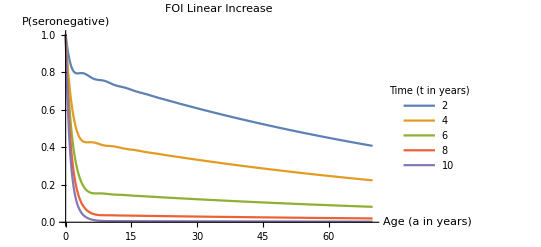

```mathematica
Plot[{t2,t4,t6,t8,t10},{a,0,70},PlotLegends->LineLegend[{"2","4","6","8","10"}, LegendLabel->"Time (t in years)"],PlotRange->{0,1},
	PlotLabel->"FOI Linear Increase", AxesLabel->{"Age (a in years)","P(seronegative)"}]
```

```mathematica
NumSol2=NDSolve[{PDE3,s[0,t]==1,s[a,0]==Exp[-λ0 a]}/.pars2,s[a,t],{a,0,70},{t,0,20}]
```

{{s[a,t]→InterpolatingFunction[…][a,t]}}

```mathematica
t2=s[a,t]/.NumSol2/.pars2/.t->2;
```

```mathematica
t4=s[a,t]/.NumSol2/.pars2/.t->4;
```

```mathematica
t6=s[a,t]/.NumSol2/.pars2/.t->6;
```

```mathematica
t8=s[a,t]/.NumSol2/.pars2/.t->8;
```

```mathematica
t10=s[a,t]/.NumSol2/.pars2/.t->10;
```

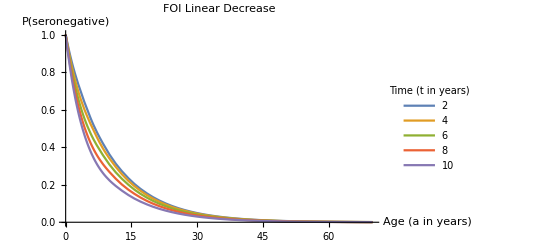

```mathematica
Plot[{t2,t4,t6,t8,t10},{a,0,70},PlotLegends->LineLegend[{"2","4","6","8","10"}, LegendLabel->"Time (t in years)"],PlotRange->{0,1},
	PlotLabel->"FOI Linear Decrease", AxesLabel->{"Age (a in years)","P(seronegative)"}]
```

## Compare to FOI as a linear function of age when time is constant

```mathematica
ODE=D[s[a],a]==-(λ0 + λ*a)*s[a]
```

s'[a]==(-a λ-λ0) s[a]

```mathematica
mysol2 = DSolve[{ODE ,s[0]==1},s[a],{a}]//FullSimplify
```

{{s[a]→ⅇ^(-1/2 a (a λ+2 λ0))}}

```mathematica
pars3={λ0->0.0001, λ->0.005};
```

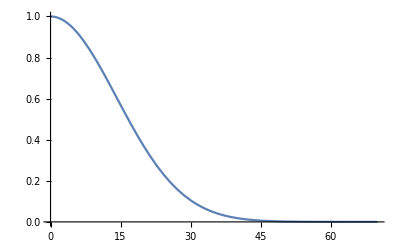

```mathematica
Plot[s[a]/.mysol2/.pars3,{a,0,70}]
```